# Homework 2

## By Marvyn Bailly

## Problem 2

Plot the system

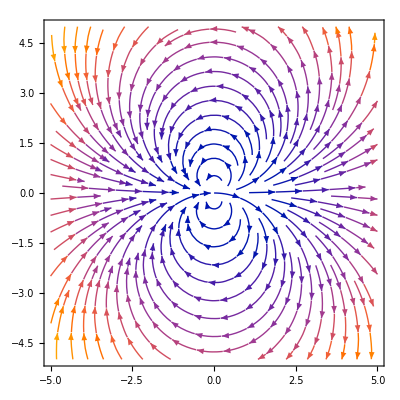

```mathematica
StreamPlot[{x^2 - y^2,2x*y},{x,-5,5},{y,-5,5}, Axes -> True]
```

## Problem 3

Solving the system

```mathematica
DSolve[a*x^3+h[x]==-h'[x]*x && h[0] == 0,h[x],x]
```

{{h[x]→-(a x^3)/4}}

Let’s see what is going on

1

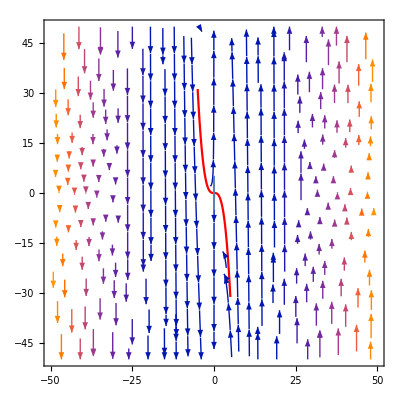

```mathematica
a=1 
streamplot = StreamPlot[{-x, y + a*x^3}, {x, -50, 50}, {y, -50, 50}, Axes -> True];
Stablineplot = Plot[-a*x^3/4, {x, -5, 5}, PlotStyle -> Red];
UnStablineplot = ParametricPlot[{0,y}, {x,-5,5},{y, -5, 5}];
Show[streamplot, Stablineplot,UnStablineplot]
```

## Problem 4

```mathematica
J = {{1,1},{1,2}}
Eigensystem[J]
```

{{1,1},{1,2}}

{{1/2 (3+√5),1/2 (3-√5)},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

```mathematica
Abs[1/2 (3-√5)] < 1
```

True

```mathematica
With[{f = Function[x, 2 x]}, 
 ParametricPlot3D[{(2 + Cos[θ]) Cos[x], (2 + Cos[θ]) Sin[x], Sin[θ]},
  {x, -Pi, Pi}, {θ, -Pi, Pi},
  MeshFunctions -> {Function[{x0, y0, z0, x, θ}, θ-f[x]], #4 &, #5 &},
  Mesh -> {2 Pi*Range[-10, 10], {0}, {0}}, 
  MeshStyle -> {Directive[Thick, ColorData[97][1]], Thin, Thin}, 
  BoundaryStyle -> None]]
```

-Graphics3D-

## Question 5

```mathematica
J = {{0,0},{0,-1}}
Eigensystem[J]
```

{{0,0},{0,-1}}

{{-1,0},{{0,1},{1,0}}}

1

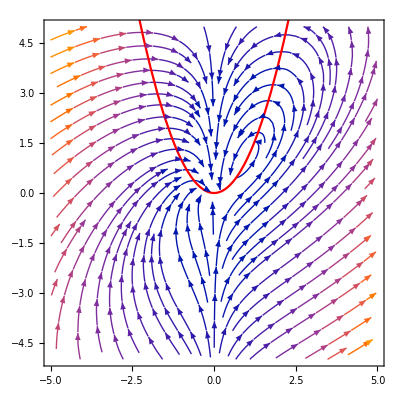

```mathematica
a=1
streamplot = StreamPlot[{a x^2 - x y, -y + x^2},{x,-5,5},{y,-5,5},Axes->True];
lineplot = Plot[x^2, {x, -5, 5}, PlotStyle -> Red];
Show[streamplot,lineplot]
```

```mathematica
Clear[a,b,α,x,y]
Expand[(a+2b x^2)*(α*x^2 - x y) /. y -> a x + b x^2]
```

-a^2 x^2-a b x^3-2 a b x^4-2 b^2 x^5+a x^2 α+2 b x^4 α

```mathematica
Manipulate[Plot[α*x^2-x^3,{x,-5,5}],{α,-5,5,1}]
```

## Question 8

```mathematica
Solve[-x+a*y+x^2*y==b-a*y-x^2*y==0,{x,y}]
```

{{x→b,y→b/(a+b^2)}}

```mathematica
J[x_,y_] = {{-1+2x*y,a+x^2},{-2*x*y,-a-x^2}}
FullSimplify[Tr[J[b,b/(a+b^2)]]]
```

{{-1+2 x y,a+x^2},{-2 x y,-a-x^2}}

1-b^2+a (-1-2/(a+b^2))

```mathematica
1/2(1-2(1/8))
```

3/8

## Question 9

### Part A

Find the fixed points

```mathematica
Clear[a]
Solve[{x(a-b*y)==0,y(-c + d*x)==0},{x,y}, Assumptions->{a,b,c,d} ∈ Reals]
```

{{x→0,y→0},{x→c/d,y→a/b}}

Find the Jacobian

```mathematica
Clear[J]
J[x_,y_] = {{a-b*y,-b*x},{d*y,-c+d*x}}
MatrixForm[J[x,y]]
```

{{a-b y,-b x},{d y,-c+d x}}

(a-b y | -b x
d y | -c+d x)

```mathematica
MatrixForm[J[0,0]]
```

(a | 0
0 | -c)

```mathematica
MatrixForm[J[c/d,a/b]]
```

(0 | -(b c)/d
(a d)/b | 0)

```mathematica
Eigensystem[J[c/d,a/b]]
```

{{-ⅈ √a √c,ⅈ √a √c},{{-(ⅈ b √c)/(√a d),1},{(ⅈ b √c)/(√a d),1}}}

### Part B

```mathematica
Solve[x(a-b*y)==0,{x,y},Assumptions->{{a,b} ∈ Reals,{x,y,a,b}>0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→ConditionalExpression[a/b, a/b∈ℝ&&a>0&&b>0&&x>0]}}

```mathematica
a = RandomReal[{1,10}]
b = RandomReal[{1,10}]
c = RandomReal[{1,10}]
d = RandomReal[{1,10}]
lb = 0;
ub = 4;
streamplot = StreamPlot[{x(a-b*y),y(-c + d*x)},{x,lb,ub},{y,lb,ub}];
yNull1 = Plot[0,{x,lb,ub},PlotStyle->Red];
xNull2 = Plot[a/b,{x,lb,ub},PlotStyle->Red];
xNull1 = ParametricPlot[{0,y}, {x,lb,ub},{y, lb, ub}];
yNull2 = ParametricPlot[{c/d,y}, {x,lb,ub},{y, lb, ub}];
Show[streamplot,yNull1,yNull2,xNull1,xNull2]
```

7.21906

3.79283

4.65532

3.48126

### Part C